```mathematica
Exit
```

## Definition

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.01;u0=10^-30;δstart=10^-10;m=100;αSch=2m;ee=DeleteDuplicates[Table[10^-n,{n,10,5,-1}]~Join~{10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1}];
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];VCou[r_]=-α/r;V[r_]=-α/r-α(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;
```

```mathematica
?V
```

```mathematica
Plot[{-0.1/r-(0.10415223038416566 ⅇ^(-0.9990999998788636 r))/r,-α/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r,-α/r},{r,0,10},PlotLegends->"Expressions"]
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=5000,wpc=50,acg=30,prc=20,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,WorkingPrecision->wpc,PrecisionGoal->prc];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.97 SetPrecision[evShifted[[n]],3],1.03 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,PrecisionGoal->prc,StepMonitor:>PrintTemporary[e]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
(*time1=SessionTime[];*)
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
(*time2=SessionTime[];*)
(*Print["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V]//Quiet;
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa,"s"];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_]:=
Module[{efunction,amplitude},efunction=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]],2];
amplitude=NIntegrate[f[r]^2/.#,{r,1.*10^-50,2000}]^-0.5&/@ef;
amplitude f[rr]/.efunction
]
```

```mathematica
δexpminus20=δ50e[10^-20,V[r]]
δexpminus15=δ50e[10^-15,V[r]]
δexpminus10=δ50e[10^-10,V[r]]
δexpminus9=δ50e[10^-9,V[r]]
δexpminus5=δ50e[10^-5,V[r]]
δ50V=δ50[V[r]]
```

NDSolve::precw: The precision of the differential equation ({{200 (1/100000000000000000000+0.01 Power[«2»]+0.0104152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.1109332855228042139377349576447953552651653036×10^-9) is less than WorkingPrecision (50.).

-2.1109332855228042108022677057082751596906858465547×10^-9

NDSolve::precw: The precision of the differential equation ({{200 (1/1000000000000000+0.01 Power[«2»]+0.0104152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.6753571690944654892223315356710604022083551877×10^-7) is less than WorkingPrecision (50.).

-6.6753571690934739674186440213313596092785600651659×10^-7

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000+0.01 Power[«2»]+0.0104152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00021108757264887988091739481701919795303860743627) is less than WorkingPrecision (50.).

-0.0002110875695136691911261541514218970208182905085214

NDSolve::precw: The precision of the differential equation ({{200 (1/1000000000+0.01 Power[«2»]+0.0104152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00066735368050678894371387504236632954508520163667) is less than WorkingPrecision (50.).

-0.00066735358143572906711110081673893792376636384714085

NDSolve::precw: The precision of the differential equation ({{200 (1/100000+0.01 Power[«2»]+0.0104152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.392237642497749201221879886481179364349343393) is less than WorkingPrecision (50.).

-0.94791476542999432327532048054853379729879260315559

{1/10000000,-0.0064911223210845317571668290486475519096572069423787}    0.339507s

{1/100000,-0.94791476542999432327532048054853379729879260315559}    0.408843s

{1/1000000000,-0.00066735358143572906711110081673893792376636384714085}    0.39045s

{1/1000000,-0.01460155814109533807709530650237779038972352880077}    0.371859s

{0.003,1.365370634609182153407777830978700659241127274778}    0.694851s

{1/100000000,-0.0021051676781619110328927105669361015047460137777448}    0.380065s

{0.001,0.93208014179939226113068427612140473965355387305601}    0.571311s

{0.007,-0.84683981706461729164525538364408525298182417916591}    0.9156544s

{0.01,-0.78771122753589553470834540907772549170624755395689}    1.521738s

{0.07,0.2668012753762507894683709776699028223563125294337}    3.536956s

{0.03,0.31818259615224733281348293541277790214275401614954}    2.245798s

{0.3,-1.1704657536305970616152711509416986589523178363479}    7.502019s

{0.1,-0.43369144810326384702914276126916306239371233294556}    4.044733s

{1,-1.42323937850538609557346508437299044095360691676}    11.915703s

{0.7,0.25798688016235417263595321881349936650701732823756}    8.8324727s

{-0.00066735358143572906711110081673893792376636384714085,-0.0021051676781619110328927105669361015047460137777448,-0.0064911223210845317571668290486475519096572069423787,-0.01460155814109533807709530650237779038972352880077,-0.94791476542999432327532048054853379729879260315559,0.93208014179939226113068427612140473965355387305601,1.365370634609182153407777830978700659241127274778,-0.84683981706461729164525538364408525298182417916591,-0.78771122753589553470834540907772549170624755395689,0.31818259615224733281348293541277790214275401614954,0.2668012753762507894683709776699028223563125294337,-0.43369144810326384702914276126916306239371233294556,-1.1704657536305970616152711509416986589523178363479,0.25798688016235417263595321881349936650701732823756,-1.42323937850538609557346508437299044095360691676}

## Determine the best 𝒶 value (using V_eff^(a^2))

```mathematica
aa={100,10,5,1,0.5,0.1,0.01,0.005(*,0.001*)};
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[a_,c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{c1start_,c1end___}]:=Module[{aaa,findroot},aaa=a;
Print[aaa];findroot=FindRoot[hhhc1[10^-10,aaa,c1]==δexpminus10,{c1,c1start,c1end},MaxIterations->200,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>Print[{c1,evnhhhc1[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a=Determinec1[#,{0}]&/@Drop[aa,0];
```

100

NDSolve::precw: The precision of the differential equation ({{200 (1.×10^-10+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080821057824064596811590613285106855878737984) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (1.×10^-10+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080821057824064596811590613285106855878737984) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{200 (1/10000000000-9.46129×10^-12 Power[«2»]+0.01 Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/1000000000000000000000000000000]==1,u[1/1000000000000000000000000000000]==1/1000000000000000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080821472113078017485620620483247706440836187) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-0.178759,-0.0004758008}

{-0.250938,-0.00021495455}

{-0.25231,-0.00018953766}

{-0.255185,-0.00011879483}

{-0.259131,0.000053047833}

{-0.258289,4.6331014×10^-6}

{-0.258201,4.1989738×10^-8}

{-0.2582,3.4479202×10^-12}

{-0.2582004485257006120104836,-6.0889274×10^-18}

{-0.25820044852570073005739807021982289353321077665407,1.6646736×10^-28}

{-0.25820044852570073005739806699249620996149732993026,-1.7×10^-51}

-0.25820044852570073005739806699249620996149732993026

10

{-0.082606,-0.00045721047}

{-0.127681,-0.00028449751}

{-0.1302,-0.00025215481}

{-0.131927,-0.00022429614}

{-0.133185,-0.00019999769}

{-0.135435,-0.0001446056}

{-0.140426,0.000094669353}

{-0.139235,0.000012877475}

{-0.139018,3.1087453×10^-7}

{-0.139012,1.8956579×10^-10}

{-0.1390124824645237788890325,-2.437502×10^-16}

{-0.13901248246452809673645204962050794534336164710616,7.3224247×10^-27}

{-0.13901248246452809673645191990938280617582388883821,2.42×10^-50}

-0.13901248246452809673645191990938280617582388883821

5

{-0.344803,-0.00033301825}

{-0.360507,-0.00024395171}

{-0.363426,-0.00021716034}

{-0.365788,-0.00019127836}

{-0.370733,-0.00011913452}

{-0.377399,0.000052429459}

{-0.375986,4.4969457×10^-6}

{-0.375841,3.9184238×10^-8}

{-0.375839,2.9922563×10^-12}

{-0.3758394846002275593833934,-1.7761809×10^-18}

{-0.37583948460022761766709636173897075863451190296249,5.40602×10^-23}

{-0.37583948460022761766529692458374106209378859593022,5.7723995×10^-24}

{-0.37583948460022761766505335848878573981353380633245,1.9286935×10^-25}

{-0.3758394846002276176650447671207165162910713965942,3.9163773×10^-29}

-0.3758394846002276176650447671207165162910713965942

1

{-0.786154,-0.00053089447}

{-2.97328,-0.00040059663}

{-3.13923,-0.0002395089}

{-3.14986,-0.00021329673}

{-3.16128,-0.00017898066}

{-3.18438,-0.000078579842}

{-3.1983,0.000017344544}

{-3.19624,5.4982086×10^-7}

{-3.19617,5.8812237×10^-10}

{-3.196168503974085917232748,2.4209858×10^-16}

{-3.1961685039740551724969093720423588791582653847097,-1.8030406×10^-23}

{-3.1961685039740551724991991013634143091081248214722,-5.1312571×10^-36}

-3.1961685039740551724991991013634143091081248214722

0.5

{-1.64932,-0.00043796048}

{-4.42953,-0.0004171832}

{-8.78655,-0.00036259319}

{-9.30427,-0.00022621381}

{-9.34442,-0.00020129229}

{-9.37385,-0.00017952861}

{-9.43134,-0.00012480545}

{-9.54145,0.000072857429}

{-9.51587,8.7610936×10^-6}

{-9.5119,1.6037355×10^-7}

{-9.51183,5.5623734×10^-11}

{-9.511825478351678140922503,-3.0071838×10^-17}

{-9.5118254783516923065761405339220973761689589345002,-3.653402×10^-19}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-9.5118254783516923065761405339220973761689589344979

0.1

{-0.518915,-0.00041068604}

{-0.784059,-0.00012233757}

{-0.813265,0.000056171166}

{-0.806967,5.0617874×10^-6}

{-0.806282,4.9162794×10^-8}

{-0.806275,4.7180148×10^-12}

{-0.8062749184398235069904559,-3.4154583×10^-19}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-0.80627491843982350699045593167905700916807745781718

0.01

{-3.78243,-0.00046300863}

{-6.72503,-0.00045048722}

{-8.27832,-0.00041925632}

{-9.25537,-0.00017280157}

{-9.30011,-0.000095226666}

{-9.3438,0.000031938248}

{-9.33559,1.8950816×10^-6}

{-9.33503,7.5087026×10^-9}

{-9.33503,1.1135222×10^-13}

{-9.335032736609854795140155,-5.8295308×10^-18}

{-9.3350327366098565046303246926302705441766312561915,-2.0113222×10^-18}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-9.3350327366098565046303246926302705441766312561883

0.005

{-10.,-0.00046384}

{-16.8563,-0.00044602179}

{-18.3642,-0.00041859065}

{-19.5594,-0.000092041101}

{-19.6061,0.000029503435}

{-19.5975,1.6416026×10^-6}

{-19.597,5.6762239×10^-9}

{-19.597,5.7687862×10^-14}

{-19.59700753965787123785422,-2.7290068×10^-18}

-19.597007539657871237854216629847135741516537111969

```mathematica
Module[{aaa,findroot,Solveδ,hhhc1δ,evnhhhc1δ},aaa=aa[[7]];
Solveδ[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k},
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
Print["Start"];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
(*Print[sol];*)
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->20,PrecisionGoal->15];
Print[δs];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
];
hhhc1δ[en_,a_,c1_?NumberQ]:=Solveδ[en,Vs1[r,a,c1]];
evnhhhc1δ[a_,c1_]:=N[hhhc1δ[10^-10,a,c1]-δexpminus10,8];
Print[aaa];findroot=FindRoot[hhhc1δ[10^-10,aaa,c1]==δexpminus10,{c1,-0},MaxIterations->200,AccuracyGoal->20,PrecisionGoal->15,WorkingPrecision->30,StepMonitor:>Print[{c1,evnhhhc1δ[aaa,c1]}]];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a
```

```mathematica
δa=Table[δ50[Vs1[r,aa[[n]],c1a[[n]]]],{n,(Length@aa)}];
Δa=Abs[δa[[#]]-δ50V]&/@Range@Length[aa];
La=Transpose@({Drop[ee,1]}~Join~{Δa[[#]]})&/@Range@Length[aa];
```

{1/1000000000,-0.00066727773187059045034368588037148669087236004600166}    0.269191s

{1/10000000,-0.0064045468170402321914679406824519944328749512230662}    0.286203s

{1/100000,-0.44243319948663762434517089579723063801905601248114}    0.299212s

{1/1000000,-0.010995508233978865846144228859221000004780045859845}    0.217134s

{1/100000000,-0.0021025225901211432497752706599041403303808953254347}    0.297662s

{0.001,0.8802486527113099964205605073732048515580483809598}    0.8447591s

{0.003,-0.79959151588530863113902613433822422531353633246825}    1.189844s

{0.01,-0.8737626550032894753737394832878961876415624313552}    2.475267s

{0.007,0.41582441571491483731193310478925397090049778203325}    2.103237s

{0.07,-0.051276066601268879015456772104425954364316413312427}    5.942247s

{0.03,0.36498078921684960679224290740569130108820202349956}    3.888858s

{0.1,-0.2634154445668447432319183986850470780427947157193}    6.389085s

{0.3,-0.86400086534483025982916873850033293837518574529912}    11.89384s

{1,-1.56119335994249257588876248835270090443013513067}    18.558086s

{0.7,0.71808299248090809145974042614763675936329195123563}    14.410688s

{1/10000000,-0.0064926221032845116969915554333309843394296353486463}    0.8327979s

{1/1000000000,-0.0006673549026197783557154189394788141030235666971735}    1.179042s

{1/100000,-0.97420091451563097990314811920397088604711925075024}    1.306133s

{1/1000000,-0.014660523853178658112623359925622451589054113428541}    0.9216545s

{1/100000000,-0.0021052137289369478685098133628028674092349117447989}    0.8586089s

{0.003,-1.0029737320146577847956135326144956283946442530498}    2.554073s

{0.001,0.93736983290946984987960914144079614963920951261315}    1.708315s

{0.01,-0.69291890549191083196678578257030699387000553878134}    4.346956s

{0.007,0.23434500449694297343735136798780856457137603404612}    4.489997s

{0.03,0.67482887888116668288622008226140471983984314439182}    8.2425277s

{0.07,0.084103226396547795555796195357291009862510050273767}    13.609256s

{0.3,-0.66607792036143831421413423227935007666609972824305}    28.431175s

{0.1,-0.022778086929653648703120031950797802025706627111895}    17.590996s

{1,-1.542955460698467618473448304502265407549608686894}    45.995786s

{0.7,0.84298029882970639652847595634012519360669909232676}    39.386758s

{1/10000000,-0.0064961359176981194936034079531691585404774795560373}    0.9776917s

{1/1000000000,-0.00066735799748706358996419524919842359400993464474502}    1.193845s

{1/100000,-1.0456347324507217138641617729319827644675365839448}    1.216861s

{1/1000000,-0.01479883140239079599871663400042239556197913959215}    1.279906s

{1/100000000,-0.0021053216043116115050036026276617105129303408380524}    1.112788s

{0.003,-0.56055878956017058806220656812415023511269148839661}    2.877036s

{0.001,0.90369577934118717897870504527911896232392594213724}    2.181543s

{0.01,-0.8892277843385575913704885797034933539579426981585}    5.340779s

{0.007,0.48051065867975859235078297578853836841422683378386}    5.028556s

{0.03,0.20919982734095812845449504284831082379056463081657}    11.033552s

{0.07,0.15659687874786817422177855780245938893564599889297}    17.384045s

{0.3,1.1831405892685607630234647116140981214272986338301}    35.071632s

{0.1,-0.68496361372974243418252479668662826050460623554776}    20.556615s

{1,-1.51702677271004012277479539498170951496718671979}    64.085512s

{0.7,1.413389915897053532090436351085920364372801872345}    46.864502s

{1/10000000,-0.0064924819459259480375358439132199894295440316846425}    1.204853s

{1/1000000000,-0.00066735477869680205446302478507628720211419938498214}    1.214842s

{1/100000,-0.97260768979077242757698107236834257929702052648547}    1.434015s

{0.003,-0.37001680771047711916488827452240200388941689232913}    2.411707s

{1/100000000,-0.0021052094109609434823364693469591634771643196945304}    1.219861s

{1/1000000,-0.014655199155544985539119220182650570553521336532328}    1.277904s

{0.001,0.92125805041325738185809830627505038291794619084341}    1.854311s

{0.007,0.51544083675411578252009791257344157930053578837222}    2.794976s

{0.01,-0.89157385219262005210232818141086152805949584186375}    4.017842s

{0.03,1.1807748995440424481407915549557350890610749213608}    5.682019s

{0.07,1.3738003234790537506544696821929071261660899043302}    10.029095s

{0.3,-0.71982449333571695247855660946893938683826220603581}    19.512972s

{0.1,-0.40359607234437733124752777169286992853547630733653}    11.447021s

{1,1.43512969249873314155591524183834465412806172593}    34.414871s

{0.7,0.55736932670136819943038491088230963670102553980777}    25.005458s

{1/1000000000,-0.00066735369418391061276817971880977791324838165511445}    1.309075s

{1/100000,-0.95019061247637941841856221232329087065372439475348}    1.355965s

{1/10000000,-0.0064912503730821493331111993570161026577915260808281}    1.489239s

{0.003,0.90175038731700296839596677303320652286896136874368}    1.928521s

{1/100000000,-0.0021051716082510204107874935935240008141582554561984}    1.568821s

{1/1000000,-0.014606615536780584139466296186585582792312660233377}    1.680324s

{0.001,0.93073722203866437205117877474369816262514168327997}    2.103467s

{0.007,1.1326374355933534153107089801267410261679098926178}    2.814939s

{0.01,-0.80887344050972461355709670943532185214564446631601}    3.494979s

{0.03,0.23816536806575954114320912455158360390430639360663}    5.005989s

{0.07,0.08657725881516825956096449858368966040342006633803}    8.2491371s

{0.3,-1.288084819554760231837427157184695889578322091233}    15.571537s

{0.1,-0.27622363857671510870109999871250713146354955686689}    8.4634732s

{1,1.33725865619972081070034813789527354867302430629}    25.974023s

{0.7,0.56003581199471861401173661540225199390328552954176}    20.408963s

{1/1000000000,-0.00066735338438263830410325987464723036653549752067127}    1.75524s

{1/10000000,-0.0064908985249490562757301380207981313753086202811063}    1.789264s

{1/100000,-0.94398043908929695219974662614328184961149267928597}    1.82429s

{0.003,-1.499556208088804079700453637619257798678358347538}    2.861022s

{1/1000000,-0.014592720499238690252729792513007175677255981083704}    1.519074s

{1/100000000,-0.002105160809448140291442724534838510180609509614}    1.563105s

{0.001,0.93381069106835983379465087693772627166569405664143}    1.527469s

{0.007,-0.33177740601569547424515572608859780606571371779172}    2.096465s

{0.01,-0.77779067629832573466526942345099974824691980674922}    2.661753s

{0.07,0.34305519611932569908123518879929825179414409425153}    6.320328s

{0.03,0.33530411842338270156948718347937341805938064818915}    4.293191s

{0.3,-1.1248689723950268225459546354261267546594803019817}    13.813767s

{0.1,-0.40561898268659705410001822896284980212535119404665}    7.9416621s

{1,-1.3812811838495839110334443789013582788133605450621}    22.562693s

{0.7,0.33394120847256501849111533853021823709468972912454}    16.120266s

{1/10000000,-0.0064908545007343145937934559899907890323580815947946}    1.770923s

{1/100000,-0.9432096341651024857493203064087509424300370608564}    1.770923s

{1/1000000000,-0.00066735334562034312338800114401872348039458452245384}    1.835527s

{1/1000000,-0.01459098149811118504028732131821026884072365072462}    1.952795s

{1/100000000,-0.0021051594583003482722010975540760432864757819985322}    2.022049s

{0.003,-1.445575141168660946700749425373769553148185160367}    3.901957s

{0.001,0.93419452661209227750280673394752160599877718890849}    2.968124s

{0.007,-0.23529774538021156519237150402855507741341057773594}    4.814903s

{0.01,-0.77421060410022139040983158049564938130221431422126}    8.1200389s

{0.07,0.47698389092285246450438644112398373084658301366441}    25.089996s

{0.03,0.34487015656021149114368450681965022717342486097946}    17.868245s

{0.1,-0.38173775459076379459547873223687614359171314494426}    27.7116s

{0.3,-1.0634516266653699505682094030693739316272861992509}    54.640962s

{1,1.2215458524135743168066634109299977619670703898169}    81.21567s

{0.7,0.4798841127217264210018058743978468823099091514929}    51.594728s

{1/100000,-0.94318074611407667401195047153169436841531306417338}    6.732531s

{1/10000000,-0.006490852849327076834364727646452334122928954188863}    7.3575357s

{1/1000000000,-0.00066735334416632392234818478631136087935882281252915}    7.5137894s

{1/100000000,-0.0021051594076171290223063470360027531623444640752394}    8.0535082s

{1/1000000,-0.014590916263861703490891187231681900791264405559081}    8.6785152s

{0.003,-1.443658546850639371755452470632657383712452811212}    18.088694s

{0.001,0.93420896826467183076073927268882672401337910220592}    12.708364s

{0.01,-0.77407311221090502715823985361956008223409446800303}    43.061704s

{0.007,-0.23207689323864089267161947951964499401774971523853}    42.783734s

{0.03,0.34525776696663626635494180203918355513214156336914}    101.976995s

{0.07,0.48586516249757343404867915466525749567643028050619}    155.027375s

{0.3,-1.060939788650641598534832025046229395909078130553}    267.85393s

{0.1,-0.38074211845873854578011448609896673929553421134518}    135.504655s

{1,1.272198346641141004160968748461250143235617793021}    368.58818s

{0.7,0.48497914406016930358396136350208711668342618513886}    200.968911s

```mathematica
Get["C:\\Users\\ASUS\\Documents\\SyntheticPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex"]
```

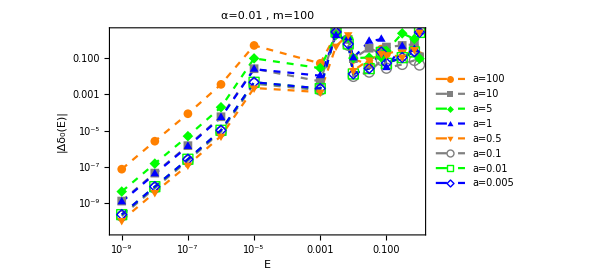

C:\Users\ASUS\OneDrive\Documents\Test_6\Test_Determine_a_Alpha=0.01&m=100.eps

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\SyntheticPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex",La];
ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->450,FrameLabel->{"E","|Δδ_0(E)|"},(*RotateLabel->False,*)PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->Placed[LineLegend[(("a="<>ToString[#])&/@aa),LegendLayout->{"Column",2}(*,LegendMarkerSize->20*),LegendMargins->{{0,0},{0,0}}(*,LegendFunction->Framed*)],(*{{},{}}*){Right,Bottom}],PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),18],FrameTicksStyle->{Bold,12}]
Evaluate["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_Determine_a_Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".eps"]
Export[%,%%];
```